# BTC-USD Drawdowns

```mathematica
Clear["Global`"];
SetDirectory[NotebookDirectory[]];
(*Buttons to hide/show code*)CloseAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];
SetOptions[#,CellOpen->False]&/@cells;];

OpenAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];
SetOptions[#,CellOpen->True]&/@cells;];

Row[{Button["Hide Code",SelectionEvaluate[CloseAllInputsCells[]]],Button["Show Code",SelectionEvaluate[OpenAllInputsCells[]]]}]
```

Hide CodeShow Code

```mathematica
settings=<|
imagemargins->20
,imagesize->1000
,labelstyle->{14}
,origindate->"Sep. 14, 2011"
,plotbackground->Lighter[LightGray,0.75]
,plotmarkers->{None,{"OpenMarkers",8},{"OpenMarkers",8}}
,plotstyle->{Automatic,Darker[Green],Lighter[Red]}
,subtitlestyle -> {15}
,ticksstyle->{16}
,titlestyle->{20,Red}
|>;
(* Function shortcuts *)
st=StringTemplate;
dollar[a_]:=st["$``"][NumberForm[a,DigitBlock->3]];
(* Default properties for generated plots *)
gridlines={
Automatic
,Join[
Range[0,10^6,5000]
,{#, Thick}& /@Range[10^4,10^6,10000]
]
};
(*imagesize=1000;*)
plotbackground=Lighter[LightGray,0.75];
updatedstr=Style[st["(updated: ``)"][DateString[]],settings[subtitlestyle]];
maniprange=Join[{1,2,3, 6, 9},Range[12,144,6]]//Reverse;
(*origindate="Sep. 14, 2011";*)
btcusd =FinancialData["BTC/USD",settings[origindate]];
nbtcusd=btcusd//Normal;
currentprice=Last[Last[nbtcusd]];
```

```mathematica
sigma=0;
peaks=FindPeaks[TimeSeriesResample[btcusd],sigma];
TimeSeriesSelect=ResourceFunction["TimeSeriesSelect"];
newpeaks=Block[{i=-∞},TimeSeriesSelect[peaks,(#2>i&&(i=#2)==i&)]];
```

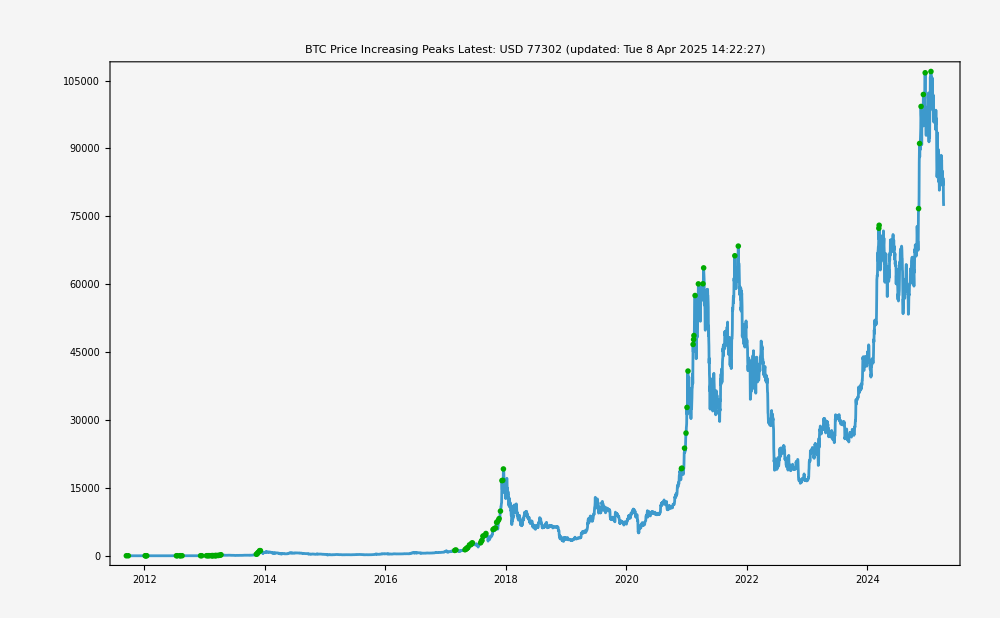

```mathematica
DateListPlot[
{btcusd,newpeaks}
,Background->plotbackground
,Joined->{True,False}
,PlotMarkers->settings[plotmarkers]
,PlotStyle->settings[plotstyle]
,ImageSize->settings[imagesize]
,ImageMargins->settings[imagemargins]
,GridLines->gridlines
,FrameTicks->All
,LabelStyle->settings[labelstyle]
,PlotLabel->Column[
{
Style[
"BTC Price Increasing Peaks"
,settings[titlestyle]
]
,Style[
"Latest: USD " <> ToString[btcusd["LastValue"]//Round]
,settings[subtitlestyle]
]
,updatedstr
}
,Center
]
]
```

```mathematica
newpeakspairs=Partition[newpeaks//Normal,2,1];
newpeakspairs=Join[newpeakspairs,{{Last[Last[newpeakspairs]],btcusd//Normal//Last}}];
```

```mathematica
dd=Join[
# 
,
low=TimeSeriesWindow[btcusd,{First[First[#]],First[Last[#]]}]//Min;
Cases[
Normal[
TimeSeriesWindow[
btcusd,{First[First[#]],First[Last[#]]}
]
]
,{_,low}
]
]&/@newpeakspairs;
```

```mathematica
displayfix[lst_]:=StringForm["`` ($``)", DateString[lst[[1]],"ISODate"],AccountingForm[lst[[2]],DigitBlock->3]];
ddx=Select[dd,(Last[Last[#]]/Last[First[#]])<0.95&];
ddpct={First[#],Last[#],PercentForm[1-(Last[Last[#]]/Last[First[#]])]}&/@ddx;
```

```mathematica
result=Manipulate[
Module[
{btcusds,ddpcts},
btcusds=TimeSeriesWindow[btcusd,{DateObject[{sinceyr,1,1}],Now}];
ddpcts=Select[ddpct,First[First[#]]>= DateObject[{sinceyr,1,1}]&& 1==1&];
dlp=DateListPlot[
{btcusds,First/@ ddpcts, #[[2]]&/@ ddpcts}
,Background->plotbackground
,Joined->{True,False, False}
,PlotMarkers->settings[plotmarkers]
,PlotStyle->settings[plotstyle]
,ImageSize->settings[imagesize]
,ImageMargins->settings[imagemargins]
,GridLines->gridlines
,FrameTicks->All
,LabelStyle->settings[labelstyle]
,PlotLabel->Column[
{
Style[
"BTC Price Drawdowns From High Peaks Since " <> ToString[sinceyr]
,settings[titlestyle]
]
,Style[
"Latest: USD " <> ToString[btcusd["LastValue"]//Round]
,settings[subtitlestyle]
]
,updatedstr
}
,Center
]
];
grd=Grid[
Join[
{Style[#,Bold]&/@{"High","Low","Pct"}}
,ReverseSortBy[
{displayfix[#[[1]]],displayfix[#[[2]]],#[[3]]}&/@ddpcts
,Last
]
]
,Frame->All
];
output=Column[{
Spacer[20]
,dlp
,Spacer[20]
,Style["BTC Price Drawdowns From High Peaks Since " <> ToString[sinceyr],"Subsection"]
,grd
,Spacer[20]
}
,Center
]
];
If[
sinceyr==2015 
,(
filename = "BTC-USD-Drawdowns_Since_"<>ToString[sinceyr]<>".jpg";
Export[filename,output];
)
];
output
,{{sinceyr,2015,Style["Since",{16, Bold}]}, Range[2011,DateValue[Now,"Year"]]}
];

result
```